# Числени методи за ОДУ

## Задача на Коши за ОДУ от първи ред. Методи на Ойлер.

## Методи на Ойлер

### Явен метод на Ойлер

-Graphics-

### Неявен метод на Ойлер

## Задача 1

Дадено е моделното уравнение


	(d u)/(d t)=-10u,0<t≤ 1,
	u(0)=1.

а) Уравнението да се реши числено, като се използва Явния метод на Ойлер при n = 4, 20, 100 и решението да се начертае в една координатна система с графиката на точното решение; (Как да пресметнем точното решение?)
б) Да се начертаят графики на абсолютната грешка в трите случая;
в) Да се направи анимация на решението при различни стойносити на n в интервала [4, 100];

```mathematica
DSolve[{u'[t]== - 10u[t], u[0]==1}, u[t], t]
```

```mathematica
{{u[t]->ⅇ^(-10 t)}}
u[t]/. DSolve[{u'[t]== - 10u[t], u[0]==1}, u[t], t]
```

{{u[t]→ⅇ^(-10 t)}}

{ⅇ^(-10 t)}

```mathematica
exactSol[t_] = u[t]/. DSolve[{u'[t]== - 10u[t], u[0]==1}, u[t], t][[1]]
```

ⅇ^(-10 t)

```mathematica
n = 4
holder = Table[0, n+1]
```

4

{0,0,0,0,0}

```mathematica
y[i] + hf[t[i], y[i]]
```

hf[t[6],y[6]]+y[6]

```mathematica
holder = Table[0, n+1]
f[u_] := -10u;
t0 = 0;
T = 1;
n = 4;
 h = (T-t0)/4;
y0 = 1;
```

{0,0,0,0,0}

```mathematica
holder[[1]] = 1
For[i=1,i≤ n, i++,

holder[[i+1]] = holder[[i]] + h*f[ holder[[i]]]
]
holder
```

1

{1,-3/2,9/4,-27/8,81/16}

```mathematica
t0 = 0; T = 1;
f[u_]:= -10u;
u0 =1;
explicitEuler[n_] := (
h = (T - t0)/ n;
y = Table[0, n+1];
y[[1]] = u0;
For[i =1, i ≤ n, i++,
y[[i+1]] = y[[i]] + h*f[y[[i]]];
];
Return[y]
)
```

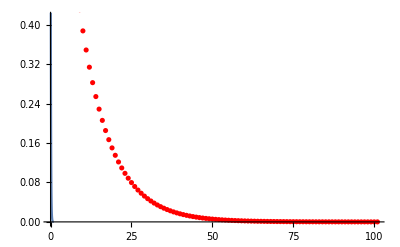

```mathematica
approx100 = explicitEuler[100];
Show[ListPlot[approx100, PlotStyle -> Red], Plot[exactSol[t], {t,0,1}]]
```

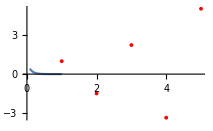
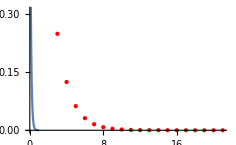
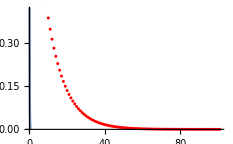
GraphicsRow[-Graphics-,-Graphics-,-Graphics-]

```mathematica
GraphicsRow[
Show[ListPlot[explicitEuler[4], PlotStyle -> Red], Plot[exactSol[t], {t,0,1}]],
Show[ListPlot[explicitEuler[20], PlotStyle -> Red], Plot[exactSol[t], {t,0,1}]],
Show[ListPlot[explicitEuler[100], PlotStyle -> Red], Plot[exactSol[t], {t,0,1}]]
]
```

## Задача 2

Да се реши моделното уравнение от Задача 1, като се използва неявният метод на Ойлер.

## Задача 3*

Да се реши моделното уравнение от Задача 1, като се използва подобреният метод на Ойлер, т.е.

(y_(i+1)-y_i)/h=(f(t_(i,)y_i)+f(t_(i+1),y_(i+1)))/2,i=1,...,n-1,
y_0=u_0

## Задача 4*

Да се имплементира методът на Нютон за приближено решаване на нелинейни уравнения и да се използва заедно с неявния метод на Ойлер, вместо вградения метод FindRoot.